## Globalized Newton’s method

```mathematica
NewtonGlob[f_,g_,h_,x0_,α0_,tol_]:=
(*f: obj function 
g: obj function gradient 
h: obj function hessian 
x0: initial point 
α0: initial step size
tol: stopping criterion *)
Module[
{sol,np,d,s,BackTracking, path,ng,iter,cluster,Δ},
sol = x0;
s[sol_]:=N[LinearSolve[h[sol[[1]],sol[[2]]],-g[sol[[1]],sol[[2]]]]];
d[sol_]:=If[-g[sol[[1]],sol[[2]]].s[sol]≥ Min[β1,β2*Norm[s[sol]]^p]*Norm[s[sol]]^2,s[sol],-g[sol[[1]],sol[[2]]]]/.{β1-> 10^-6,β2-> 10^-6,p-> 0.1};

(*determine stepsize by backtracking method (Armijo Condition)*)
BackTracking[sol_]:=Module[
{ϕ0,ϕ1,x1,t,αcount},
ϕ0=f[sol[[1]],sol[[2]]];
t=α0;
x1=sol+t*d[sol];
ϕ1=f[x1[[1]],x1[[2]]];
αcount=1;
While[ϕ1>ϕ0-t *γ* Norm[d]^2&& αcount≤100,
t=σ t/.σ-> 0.5;
αcount+=1;
x1=sol+t*d[sol];
ϕ1=f[x1[[1]],x1[[2]]];]/.γ-> 0.1;
t
];

np[sol_]:=sol+BackTracking[sol]*d[sol];(*find next x*)
path=NestWhileList[np,sol, Norm[g[#[[1]],#[[2]]]]>tol& ];(*Main loop*)
ng=Map[Norm[g[#[[1]],#[[2]]]]&,path];(*Norm of gradient*)
iter=Table[i,{i,0,Length[path]-1}];
cluster[path_]:=path[[-1]];(*find the convergence point of seq of Xs, i.e. global minimizer*)
Δ=Map[Norm[#]&,Map[#-cluster[path]&,path]];(*Difference between each x and the global minimizer*)
NewtonGlob[TableHeadings]={"ITER","X_k","G.NORM","Residue"};
{TableForm[Transpose[{iter,path, ng,Δ}],TableHeadings->{None, NewtonGlob[TableHeadings]}],
(*ListLinePlot[Map[f[#[[1]],#[[2]]]&,path],PlotRange->All,AxesLabel->{"Iter","fValue"},ImageSize->Medium,PlotStyle->Red,PlotLabel-> Row[{"Initial Point = ",x0}]],*)
ListLogPlot[ng,Joined->True,PlotRange->All,PlotStyle->Red,ImageSize->Medium,AxesLabel->{"Iter","G.NORM"},PlotLabel->Row[{"Norm of gradient"}]],
ListLogPlot[Δ,Joined->True,PlotRange->All,ImageSize->Medium,AxesLabel->{"Iter","Δ"},PlotLabel->Row[{"Norm of x_k-x^*"}]]}
];
```

## Demo

```mathematica
f1[x_,y_]:=x+((5-y) y-2) y-13
f2[x_,y_]:=x+((y+1) y-14) y-29
f[x_,y_]:=f1[x,y]^2+f2[x,y]^2
```

```mathematica
g[x_?NumberQ,y_?NumberQ]=Map[D[f[x,y],#]&,{x,y}];(*Gradient of f*)
h[x_?NumberQ,y_?NumberQ]=Outer[D[f[x,y],##]&,{x,y},{x,y}];(*Hessian of f*)
```

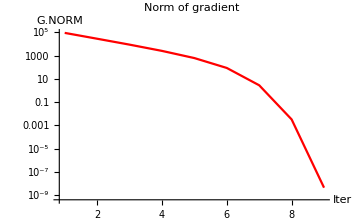
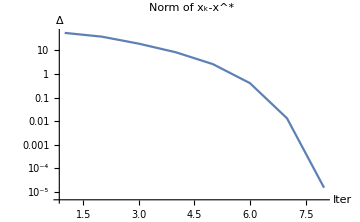
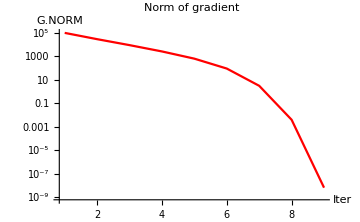
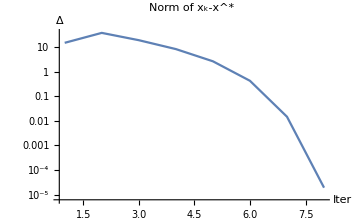
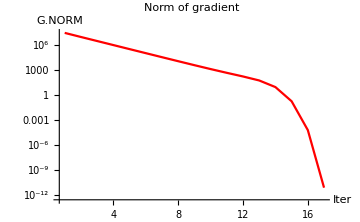
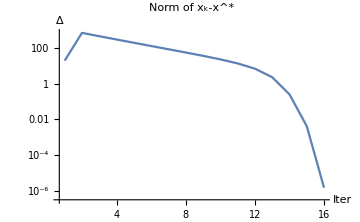
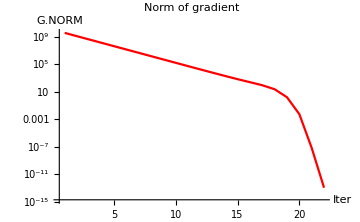
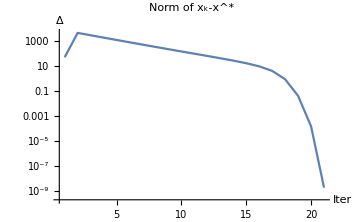
{Time(in seconds) and Result | Convergence Plot | 
0.029897 |  | 
ITER | X_k | G.NORM | Residue
0 | -50
7 | 20 √20638865 | 55.0818
1 | -33.0923
5.91448 | 28529. | 38.1404
2 | -14.224
5.09942 | 8851.62 | 19.2554
3 | -3.30235
4.52789 | 2566.91 | 8.31911
4 | 2.38775
4.1799 | 619.549 | 2.61844
5 | 4.59074
4.02965 | 87.3227 | 0.410329
6 | 4.98668
4.00099 | 2.82788 | 0.0133565
7 | 4.99998
4. | 0.00327528 | 0.0000154081
8 | 5.
4. | 4.39994×10^-9 | 0. | -Graphics- | -Graphics-,Time(in seconds) and Result | Convergence Plot | 
0.021354 |  | 
ITER | X_k | G.NORM | Residue
0 | 20
7 | 1020 √9685 | 15.2971
1 | -33.8404
5.93648 | 29280.5 | 38.8887
2 | -14.5548
5.11535 | 9098.22 | 19.5866
3 | -3.48711
4.53847 | 2644.71 | 8.50417
4 | 2.3019
4.18553 | 642.67 | 2.70447
5 | 4.56732
4.03132 | 92.4011 | 0.43381
6 | 4.98517
4.0011 | 3.14782 | 0.0148703
7 | 4.99998
4. | 0.00405701 | 0.0000190859
8 | 5.
4. | 6.75367×10^-9 | 0. | -Graphics- | -Graphics-,Time(in seconds) and Result | Convergence Plot | 
0.024453 |  | 
ITER | X_k | G.NORM | Residue
0 | 20
-18 | 20 √1823461376465 | 19.1379
1 | -667.911
-14.3182 | 8.72387×10^6 | 679.456
2 | -431.534
-11.3681 | 2.85699×10^6 | 443.07
3 | -278.519
-9.01762 | 935596. | 290.046
4 | -178.991
-7.14819 | 306447. | 190.506
5 | -113.976
-5.66459 | 100457. | 125.48
6 | -71.2633
-4.49005 | 33004. | 82.7541
7 | -42.9758
-3.562 | 10899.3 | 54.4538
8 | -24.0161
-2.82853 | 3639.24 | 35.4815
9 | -11.0686
-2.2454 | 1241.57 | 22.5218
10 | -1.97299
-1.7743 | 439.125 | 13.4145
11 | 4.61158
-1.38545 | 160.749 | 6.81873
12 | 9.15736
-1.07898 | 53.2959 | 2.26276
13 | 11.1628
-0.920957 | 8.58041 | 0.251176
14 | 11.4086
-0.897241 | 0.171424 | 0.0041689
15 | 11.4128
-0.896805 | 0.0000594852 | 1.52453×10^-6
16 | 11.4128
-0.896805 | 7.48058×10^-12 | 0. | -Graphics- | -Graphics-,Time(in seconds) and Result | Convergence Plot | 
0.02764 |  | 
ITER | X_k | G.NORM | Residue
0 | -8
-50 | 4 √1000795398163617041 | 52.8013
1 | -4764.
-39.8864 | 1.30886×10^9 | 4775.57
2 | -3069.6
-31.7945 | 4.28826×10^8 | 3081.17
3 | -1980.19
-25.3255 | 1.40488×10^8 | 1991.76
4 | -1278.8
-20.1555 | 4.60212×10^7 | 1290.36
5 | -826.554
-16.0261 | 1.5074×10^7 | 838.103
6 | -534.42
-12.7301 | 4.93681×10^6 | 545.961
7 | -345.278
-10.1024 | 1.61669×10^6 | 356.809
8 | -222.46
-8.01049 | 529455. | 233.981
9 | -142.411
-6.34848 | 173472. | 153.92
10 | -89.9793
-5.03112 | 56916.4 | 101.476
11 | -55.4047
-3.98938 | 18739. | 66.889
12 | -32.3813
-3.16652 | 6217.11 | 43.8529
13 | -16.8186
-2.51486 | 2095.31 | 28.2777
14 | -6.04983
-1.99329 | 726.819 | 17.497
15 | 1.6449
-1.56689 | 262.565 | 9.79084
16 | 7.2016
-1.21622 | 94.7112 | 4.22327
17 | 10.5201
-0.975167 | 24.6725 | 0.896081
18 | 11.3715
-0.901112 | 1.68447 | 0.0414565
19 | 11.4126
-0.89682 | 0.00577816 | 0.000148465
20 | 11.4128
-0.896805 | 7.07625×10^-8 | 1.75302×10^-9
21 | 11.4128
-0.896805 | 1.14033×10^-13 | 0. | -Graphics- | -Graphics-}

```mathematica
Table[TableForm[Timing[NewtonGlob[f,g,h,i,1,10^-8]],TableHeadings->{None, {"Time(in seconds) and Result","Convergence Plot"}}],{i,{{-50,7},{20,7},{20,-18},{-8,-50}}}]
```